# Homework 7 - Jacob DeFilippis

## Question 1

```mathematica
Part A
```

```mathematica
due to Rayliegh formulas
```

```mathematica
sphericalbessel[n_]=(-1)^n D[Sin[x]/x,{x,n}]
```

(-1)^n ∂_{x,n} Sin[x]/x

```mathematica
sphericalneumann[n_] = (-1)^n D[Cos[x]/x,{x,n}]
```

(-1)^n ∂_{x,n} Cos[x]/x

```mathematica
Part B
```

```mathematica
sphericalbessel[0]
```

Sin[x]/x

```mathematica
sphericalbessel[1]
```

-Cos[x]/x+Sin[x]/x^2

```mathematica
sphericalbessel[10]
```

-(3628800 Cos[x])/x^10+(604800 Cos[x])/x^8-(30240 Cos[x])/x^6+(720 Cos[x])/x^4-(10 Cos[x])/x^2+(3628800 Sin[x])/x^11-(1814400 Sin[x])/x^9+(151200 Sin[x])/x^7-(5040 Sin[x])/x^5+(90 Sin[x])/x^3-Sin[x]/x

```mathematica
sphericalneumann[0]
```

Cos[x]/x

```mathematica
sphericalneumann[1]
```

Cos[x]/x^2+Sin[x]/x

```mathematica
sphericalneumann[10]
```

(3628800 Cos[x])/x^11-(1814400 Cos[x])/x^9+(151200 Cos[x])/x^7-(5040 Cos[x])/x^5+(90 Cos[x])/x^3-Cos[x]/x+(3628800 Sin[x])/x^10-(604800 Sin[x])/x^8+(30240 Sin[x])/x^6-(720 Sin[x])/x^4+(10 Sin[x])/x^2

```mathematica
Part C
```

```mathematica
Series[sphericalbessel[10],{x,0,3}]
```

-1/11+x^2/26+O[x]^4

```mathematica
Series[sphericalneumann[10],{x,0,3}]
```

3628800/x^11+x/12-x^3/84+O[x]^4

```mathematica
Part D
```

```mathematica
sphericalbessel[1]
```

-Cos[x]/x+Sin[x]/x^2

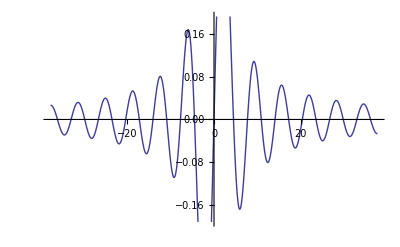

```mathematica
Plot[-Cos[x]/x+Sin[x]/x^2,{x,-37.69911184307752,37.69911184307752}]
```

```mathematica
sphericalneumann[1]
```

Cos[x]/x^2+Sin[x]/x

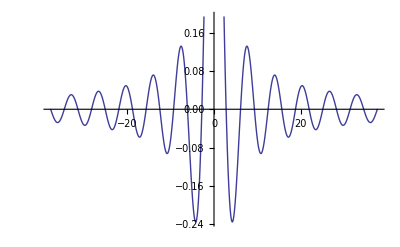

```mathematica
Plot[Cos[x]/x^2+Sin[x]/x,{x,-37.69911184307752,37.69911184307752}]
```

## Question 2

2 Question

```mathematica
Series[Tanh[x],{x,0,20}]
```

x-x^3/3+(2 x^5)/15-(17 x^7)/315+(62 x^9)/2835-(1382 x^11)/155925+(21844 x^13)/6081075-(929569 x^15)/638512875+(6404582 x^17)/10854718875-(443861162 x^19)/1856156927625+O[x]^21

```mathematica
InverseSeries[%]
```

x+x^3/3+x^5/5+x^7/7+x^9/9+x^11/11+x^13/13+x^15/15+x^17/17+x^19/19+O[x]^21

## Question 3

3 Question

```mathematica
Part(A)
```

A Part

```mathematica
Integrate[(x^4 Exp[x])/(Exp[x]-1)^2,{x,0,Infinity}]
```

(4 π^4)/15

```mathematica
Part (B)
```

## We reform the integral and take the limit as the θ/d defined as p goes to 0

```mathematica
N[Limit[9*(1/p^3) Integrate[(y^4)/(2*(Series[Cosh[y],{y,0,10}] -1)),{y,0,p}],p->0],4]
```

3.

```mathematica
Part  C
```

```mathematica
f[o_] =N[Limit[9*(1/p^3) Integrate[(y^4)/(2*(Series[Cosh[y],{y,0,10}] -1)),{y,0,p}],p->o],4]
```

3.-0.15 o^2+0.005357 o^4-0.0001653 o^6+4.735×10^-6 o^8

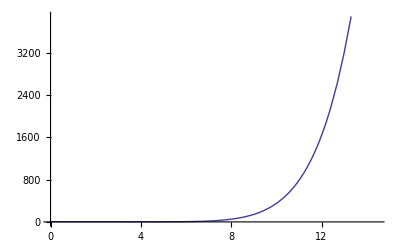

```mathematica
Plot[3.`4.-0.15`4. o^2+0.00535714285714285714285714285714285714`4. o^4-0.00016534391534391534391534391534391534`4. o^6+4.73484848484848484848484848484848`4.*^-6 o^8,{o,0,14.474937289114926}]
```

## Question 4

### Part A

```mathematica
mag[j_]:=m /.FindRoot[m-Tanh[j m],{m,.5}]
```

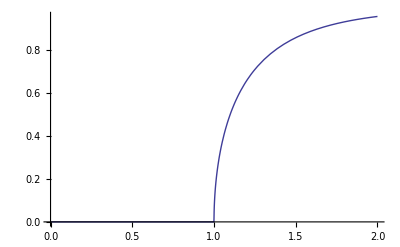

```mathematica
Plot[mag[j],{j,0,2}]
```

j is defined as J/T  once T > J , when J/T < 1 the value is equal to zero

## Part B

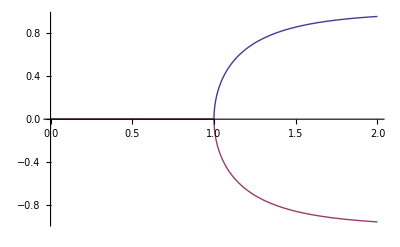

```mathematica
magalt[j_]:=m /.FindRoot[m-Tanh[j m],{m,-.5}]
Plot[{mag[j],magalt[j]},{j,0,2}]
```

There is a root on the negative side and positive side which both give equal and opposite value for m